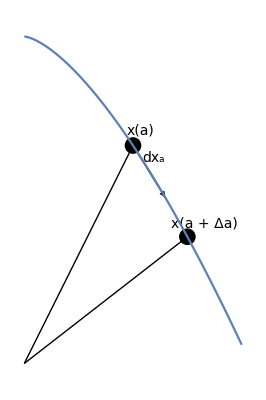

{oneParameterDifferentialFig1.eps,oneParameterDifferentialFig1pn.png}

```mathematica
to[start_,end_,ss_:0]=start+(end-start) (1+ss/Norm[end-start]);
setback = {0.4, 0.4} ;
o = {0,0};
f = 3 - #^1.5 & ;
pair = {#,f[#]} &;
bold = Style[ #, Bold] &;
p = Plot[f[x], {x,0,2}] ;
g = Show[
Graphics[{
Thick,Arrowheads[0.08],
Arrow[{o,pair[1]}],
Arrow[{o,pair[1.5]}],
Arrow[{pair[1],pair[1.3]}],
Text[
Style[Row[{bold[x],"(a)"}], FontSize-> 14],
to[ o, pair[1], 0.15]],
Text[
Style[Subscript[bold[dx],"a"], FontSize-> 14],
to[ pair[1], pair[1.05], 0.15]*1.05 ],
Text[
Style[Row[{bold[x],"(a + Δa)"}], FontSize-> 14],
to[ o, pair[1.5], 0.2]],
PointSize[0.03],
Point[ pair[1]],
Point[pair[1.5]]
}]
, p 
]

peeters`exportForLatex["oneParameterDifferentialFig1", g]
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures" ]
```

/Users/pjoot/project/figures